Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

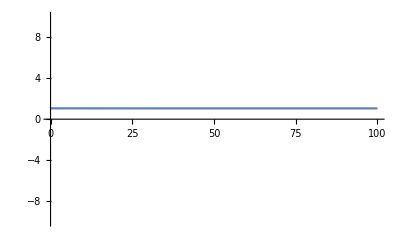

Time elapsed: 0.0648191

```mathematica
Clear["Global`*"]
time=AbsoluteTime[];

(*Массив значений энергий*)
omegaVal={};

(*Интервал энергий*)
lowerBoundLow =-1;
upperBoundLow =1.5;

lowerBoundHigh=1.55;
upperBoundHigh=4;

step =0.1;


(*С каких углов считаем излучение*)
lowerAngle=0.1;
upperAngle=Pi/2.01;
nSteps=6;

(*Параметры АЛП*)
g=6*10^(-20);
m=10^(-8);

(*Конфигурация поля*)
angleObserver = Pi/3;
BSurf = 15*10^12;
R0 = 12;
period =7;

(*Конфигурация точки излучения*)
(*По x мы итерируемся, r - расстояние от поверхности звезды*)
r:=Sqrt[(R0 Sin[angleEmission]+x)^2 + (R0 Cos[angleEmission]+x Cot[alpha+angleEmission])^2];
angleIteration:=ArcTan[(R0 Sin[angleEmission]+x)/(R0 Cos[angleEmission]+x Cot[alpha+angleEmission])];

startingInclination:=Solve[1-Cos[alphaStartingInclination]==(1-Cos[angleObserver - angleEmission])(1-4.134/R0),alphaStartingInclination];

(*Радиус светового цилиндра*)
Rlc=47713*period;
upperLimit:=Rlc;

(*Значения поля (диполь)*)
(*Множитель плотности GJ*)
bRep:={bRad->BSurf*Cos[angleIteration]*(R0/r)^3,
	bTheta->0.5*BSurf*Sin[angleIteration]*(R0/r)^3,
	bPhi->0,
	GJfactor->1};


(*Элементы матрицы М*)
deltaMTheta:=5.0*10^7*bTheta*g;
deltaMPhi:=5.0*10^7*bPhi*g;
deltaMass:=2.5*10^9*m^2*(1/ω);
deltaPlasma:=GJfactor*3.1*10^(-12)*(bRad*Cos[angleIteration]-bTheta*Sin[angleIteration])*(1/period)*(1/ω);
deltaCEDTheta:=-4.5*10^(-22)*ω*bTheta^2;
deltaCEDPhi:=-4.5*10^(-22)*ω*bPhi^2;

(*Матрица М*)
mat:={{deltaPlasma+deltaCEDTheta,0,deltaMTheta},
	{0,deltaPlasma+deltaCEDPhi,deltaMPhi},
	{deltaMTheta,deltaMPhi,deltaMass}}/.bRep;

(*Матрица плотности ρ*)
rmat[x_]:={{r11[x],r12[x],r13[x]},{r21[x],r22[x],r23[x]},{r31[x],r32[x],r33[x]}};

(*Список начальных условий*)rmat0={{r11[0]==1,r12[0]==0,r13[0]==0},{r21[0]==0,r22[0]==0,r23[0]==0},{r31[0]==0,r32[0]==0,r33[0]==0}};


(*Энергия на поверхности*)
ω0:=10^(0);

(*С красным смещением*)
ω:=ω0*Sqrt[(1-(4.134/R0))/(1-(4.134/r))];


(*Угол от 0 до 2.01*)
angleEmission=angleObserver+0.01;

unsignedAngles=alphaStartingInclination/.startingInclination[[2]];
sumAngles=unsignedAngles+angleEmission;

signs=Sign[angleObserver-unsignedAngles-angleEmission];
alpha=unsignedAngles*signs;

(*Print["angleEmission ",angleEmission," unsignedAngles ",unsignedAngles," sumAngles ",sumAngles," signs ",signs," alpha", alpha];*)
(*Решаем систему*)
p=Plot[angleIteration,{x,0,100},PlotRange->{{0,100},{-10,10}}];
Show[p]



Print["Time elapsed: ",AbsoluteTime[]-time];
```